# PG onset of thermal convection

This notebook requires the user to make some choices along the way: simple execution of the whole thing will likely not result in the desired outcome.

- In Section “Definitions/Parameters”, the user needs to set numerical and physical parameters

- Parallel Kernels are launched and closed executing the chapters “Launching parallel kernels!” and “Closing parallel kernels!”. Since ParallelTable is used in the calculation of the matrices, parallel kernels may be launched even if not explicitly required

- In “Calculate/load the matrices” the user can decide whether to calculate the matrices (Section “Calculate the PG matrices (Gauss-Jacobi)”) or load them from previous calculations (Section “Load the PG matrices (GJ)”) . The former loads existing matrices anyway, but runs consistency checks, so the latter section is much faster if the user is sure of the quality of the existing matrices.

- In section “Solving the eigenvalue problem/Specify matrices” the user needs to execute the subsections that correspond to either non-slip or stress-free boundary conditions

- The sections “Solve the eigenvalue problem: systematic approach/Find Critical Ra/Visual solver ...” do not need to be run. They give plots of the growth rate of the mode as a function of Ra. They are useful to find good initial guesses for Ra, but the real solver is in   “Solve the eigenvalue problem: systematic approach/Find Critical Ra/Find critical Ra”

## Libraries, packages and notebook options

```mathematica
SetOptions[$FrontEndSession,"ExportTypesetOptions"->{"PageWidth"->500}]
```

```mathematica
Needs["Optimize`"]
```

```mathematica
Needs["NumericalDifferentialEquationAnalysis`"]
```

```mathematica
<<MaTeX`
```

## Launching parallel kernels!

```mathematica
LaunchKernels[];
ParallelNeeds["NumericalDifferentialEquationAnalysis`"]
```

## Definitions

## Parameters

Azimuthal wavenumber

```mathematica
m0=1
```

1

Ekman and thermal Prandtl numbers

```mathematica
Clear[Pr]
Clear[Ek]
Pr=SetPrecision[Rationalize[0.001],50]
Ek=SetPrecision[Rationalize[5*10^(-5)],50]
```

0.001

0.00005

Bounding estimates for critical Rayleigh number (Restimate1 and Restimate2) and interval at which the growth rate is plotted (dR1)

```mathematica
Restimate1 = 19;
Restimate2 = 21;
dR1 = 0.2;
```

Drift frequency estimate

```mathematica
omegaestimate=-0.17;
```

Degrees if freedom, N. The spatial resolution of the radial basis functions

```mathematica
dof=15
```

15

When loading pre-calculated matrices, they have been calculated with the following resolution

```mathematica
doffile=15;
```

Save the calculated matrices for future use?

```mathematica
flagSave=True
```

True

eigTol = Spectral convergence parameter below which a solution is considered converged.
acc = solution accuracy below which iterative methods are stopped

Need to be played a bit with. For “easy” solutions (for which a direct solver would do) these numbers can be large (e.g. 10^-2)

```mathematica
eigTol=10^(-2)//N;
acc = 10^(-2)//N;
```

Max number of iterations for the root finding algorithms

```mathematica
maxIter = 5;
```

Arnoldi solver parameters: relative distance from intial guess and number of solutions calculated

```mathematica
accEV = 0.1;
Nsols=10;
```

Minimal working precision

```mathematica
prec1=120;
```

Number of random points at which solution is calculated for 2D visualisation purposes.

```mathematica
Npoints=10^4;
```

### Folders to look for previously calculated matrices

Local folder

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
folder1 =NotebookDirectory[]<> "Matrices/";
```

```mathematica
foldersList = {folder1}
```

{/Users/stefanomaffei/Documents/Papers/2017_PG_convection/Mathematica/PG-basics/Matrices/}

```mathematica
saveFolder = folder1;
```

The files looked for have the following syntax:

fileName=StringJoin[filePre,precStr,”_m”,ToString[m0],”dof”]

where filePre is the name of the matrix saved and precStr in an optional string (empty by default) that can be used to indicate, for example, higher precision files

```mathematica
str2D=StringJoin["_m",ToString[m0],"dof",ToString[doffile],".wdx"]
```

_m1dof15.wdx

```mathematica
precStr="";
```

```mathematica
(*precStr="_precmin120"*)
```

## Define quadratures

### Gauss-Jacobi quadrature

```mathematica
colweight[N_,a_,b_] := -(2N + a+b+2)/(N+a+b+1)*(Gamma[N+a+1]*Gamma[N+b+1])/(Gamma[N+a+b+1]Factorial[N+1])*(2^(a+b)/(D[JacobiP[N,a,b,x],x]*JacobiP[N+1,a,b,x]));
```

```mathematica
GJQuadratureSingle[Integrand_,alphaJ_,betaJ_,i0_,j0_,m0_,colN_,prec_] := 
 Module[{tmp,tmp2,tmp3,sol,rlocation},

tmp=Integrand;
tmp2=1/(2 √(2(x+1)))*tmp/.s->  √((x+1)/2);
tmp3=tmp2/((1-x)^alphaJ (1+x)^betaJ);

sol=Solve[JacobiP[colN,alphaJ, betaJ,x]==0 ,x];
rlocation=N[x /.#&/@sol,prec];

Total[2*Pi*colweight[colN,alphaJ,betaJ]*tmp3/.m->m0/.i-> i0/.j-> j0/.x-> rlocation]
  ];
```

```mathematica
GJQuadratureSingleOpt[Integrand_,alphaJ_,betaJ_,i0_,j0_,m0_,colN_,prec_] := 
 Module[{tmp,tmp2,tmp3,sol,rlocation,opt},

tmp=Integrand;
tmp2=1/(2 √(2(x+1)))*tmp/.s->  √((x+1)/2);
tmp3=tmp2/((1-x)^alphaJ (1+x)^betaJ);

sol=Solve[JacobiP[colN,alphaJ, betaJ,x]==0 ,x];
rlocation=N[x /.#&/@sol,prec];

opt=Experimental`OptimizeExpression[tmp3];

list={m->m0,i-> i0,j-> j0,x-> rlocation};

Total[(opt/.list//First)*(2*Pi*colweight[colN,alphaJ,betaJ]/.list)]

  ];
```

```mathematica
GJQuadrature[Integrand_,alphaJ_,betaJ_,imin_,imax_,jmin_,jmax_,m0_,colN_,prec_] := 
 Module[{tmp,tmp2,tmp3,sol,rlocation,i0,j0},

tmp=Integrand;
tmp2=1/(2 √(2(x+1)))*tmp/.s->  √((x+1)/2);
tmp3=tmp2/((1-x)^alphaJ (1+x)^betaJ);

sol=Solve[JacobiP[colN,alphaJ, betaJ,x]==0 ,x];
rlocation=N[x /.#&/@sol,prec];

ParallelTable[Total[2*Pi*colweight[colN,alphaJ,betaJ]*tmp3/.m->m0/.i-> i0/.j-> j0/.x-> rlocation],{i0,imin,imax},{j0,jmin,jmax}]
  ]
```

```mathematica
GJQuadratureOpt[Integrand_,alphaJ_,betaJ_,imin_,imax_,jmin_,jmax_,m0_,colN_,prec_] := 
 Module[{tmp,tmp2,tmp3,sol,rlocation,i0,j0,opt,list},

tmp=Integrand;
tmp2=1/(2 √(2(x+1)))*tmp/.s->  √((x+1)/2);
tmp3=tmp2/((1-x)^alphaJ (1+x)^betaJ);

sol=Solve[JacobiP[colN,alphaJ, betaJ,x]==0 ,x];
rlocation=N[x /.#&/@sol,prec];

opt=Experimental`OptimizeExpression[tmp3];

ParallelTable[Total[(2*Pi*colweight[colN,alphaJ,betaJ]/.m->m0/.i-> i0/.j-> j0/.x-> rlocation)*(opt/.m->m0/.i-> i0/.j-> j0/.x-> rlocation//First)],{i0,imin,imax},{j0,jmin,jmax}]
  ]
```

```mathematica
CalculateMatrices[Integrand_,fileName_,foldersList_,alphaJ_,betaJ_,m0_,colN_,prec_,dof_,saveFolder_,flagSave_]:=Module[{List1,nums,dofsList,idx,dofsFiles,impMat,check1,dofsCheck},

List1 = FileNames[StringJoin[fileName,"*.*"],foldersList];
Print[fileName];
If[List1=={},

Print["No previously saved matrix was found"];
Mat=GJQuadrature[Integrand,alphaJ,betaJ,1,dof,1,dof,m0,colN,prec];
(*save new matrix*)
If[flagSave==True,Export[StringJoin[saveFolder,fileName,ToString[dof],".wdx"], Mat]];
,

Print["Previously saved matrices were found"];

nums =StringCases[List1,DigitCharacter..];

dofsList=ToExpression[nums[[All,-1]]];

(*this might be generalised, take only the first for now*)

idx=Position[dofsList,Max[dofsList]][[All,1]][[1]];

dofsFiles = dofsList[[idx]];

Print[List1[[idx]]];

impMat =Import[List1[[idx]]] ;

(*to check that the matrix is valid*)

dofsCheck = Min[dof,dofsFiles];

check1=GJQuadratureSingle[Integrand,alphaJ,betaJ,dofsCheck,dofsCheck,m0,colN,prec];

Mat=Table[0,{i,dof},{j,dof}];

If[N[Abs[check1-impMat[[dofsCheck,dofsCheck]]]]<10.^(-16),
Print["Loaded matrix is valid"];
If[dofsFiles<dof,

Print["Calculating missing dofs"];

Mat[[1;;dofsFiles,1;;dofsFiles]] = impMat;

Mat[[dofsFiles+1;;dof,1;;dof]]=GJQuadrature[Integrand,alphaJ,betaJ,dofsFiles+1,dof,1,dof,m0,colN,prec];

Mat[[1;;dofsFiles,dofsFiles+1;;dof]]=GJQuadrature[Integrand,alphaJ,betaJ,1,dofsFiles,dofsFiles+1,dof,m0,colN,prec];
(*save new matrix*)
If[flagSave==True,Export[StringJoin[saveFolder,fileName,ToString[dof],".wdx"], Mat]];
,
Print["Loaded matrix contains what is needed"];
Mat = impMat[[1;;dof,1;;dof]];
],
Print["Matrix not valid; recalculating it all"];
Mat=GJQuadrature[Integrand,alphaJ,betaJ,1,dof,1,dof,m0,colN,prec];
(*save new matrix*)
If[flagSave==True,Export[StringJoin[saveFolder,fileName,ToString[dof],".wdx"], Mat]];
]
];

Mat
]
```

## Define velocity. Columnar modes

```mathematica
H=Sqrt[1-s^2];
β=(1/H)D[H,s];
```

Analytical solution for PG modes in a sphere

```mathematica
omegapg[m_,N_]:=-m/( N*(2*N+2*m+1)+m/2+m^2/4 )
```

```mathematica
omegaqg[m_,N_]:=-m/( N*(2*N+2*m+1)+m/2+m^2/6 )
```

```mathematica
omegaav[m_,N_]:=-m/( N*(2*N+2*m+1)+m/2 )
```

Compiling the norm functions in advance does not seem to help with the speed

```mathematica
Psi1[m_,N_]:=Sqrt[-omegapg[m,N]/(4*Pi*m)]s^m H^3  JacobiP[N-1,3/2,m,2 s^2-1]/Sqrt[(1/2)Gamma[(N-1)+5/2]Gamma[(N-1)+m+1]/( Factorial[(N-1)](2 (N-1) + 5/2 + m)Gamma[(N-1)+5/2+m])];
```

Non-normalised version:

```mathematica
Psi2[m_,N_]:=s^m H^3  JacobiP[N-1,3/2,m,2 s^2-1]
```

```mathematica
Ue=(1/H)Curl[{0,0,Psi[s] Exp[ⅈ m phi]},{s,phi,z},"Cylindrical"];
```

```mathematica
Umerid= {ⅈ m Psi[s]/(s H),-(1/H)D[Psi[s],s],-ⅈ z m Psi[s]/H^3}//Simplify;
```

```mathematica
U=Umerid Exp[ⅈ m phi] //Simplify;
```

```mathematica
UmeridConjugate={-ⅈ m Psi[s]/(s H),-(1/H)D[Psi[s],s],ⅈ z m Psi[s]/H^3}//Simplify;
```

```mathematica
UConjugate=UmeridConjugate Exp[-ⅈ m phi] //Simplify;
```

```mathematica
Uspher = TransformedField["Cylindrical"->"Spherical",U,{s,phi,z}->{r,th,ph}]//Simplify;
```

```mathematica
omegaSpherical=Curl[Uspher,{r,th,ph},"Spherical"]//Simplify;
```

### Quantities I need in spherical coordinates (does not seem to work)

```mathematica
Psi1Spherical[r_,th_,m_,N_]:=TransformedField["Cylindrical"->"Spherical",Psi1[m,N],{s,phi,z}->{r,th,ph}]
```

```mathematica
U1[s_,phi_,z_,m1_,N_] := U/.Psi[s]->Psi1[m1,N]/.D[Psi[s],s]->D[Psi1[m1,N],s]/.m->m1
```

```mathematica
U1Spherical[r_,th_,ph_,m_,N_]:=TransformedField["Cylindrical"->"Spherical",U1[s,phi,z,m,N],{s,phi,z}->{r,th,ph}]
```

```mathematica
omega1Spherical[r_,th_,ph_,m_,N_]:=Curl[U1Spherical[r,th,ph,m,N],{r,th,ph},"Spherical"]
```

#### No-slip quantities

```mathematica
Z1[theta_,m_,N_]:= - Sqrt[ⅈ (omegapg[m,N]-2Cos[theta])]
Z2[theta_,m_,N_]:= - Sqrt[ⅈ (omegapg[m,N]+2Cos[theta])]
```

```mathematica
Z1cyl[z_,m_,N_]:= - Sqrt[ⅈ (omegapg[m,N]-2z)]
Z2cyl[z_,m_,N_]:= - Sqrt[ⅈ (omegapg[m,N]+2z)]
```

```mathematica
Ubl1[zeta_,th_,ph_,m_,N_]:=-(1/2)((U1Spherical[r,th,ph,m,N] + ⅈ{1,0,0}.U1Spherical[r,th,ph,m,N])/.r->1)Exp[zeta Z1[th,m,N]] -(1/2)((U1Spherical[r,th,ph,m,N] - ⅈ{1,0,0}.U1Spherical[r,th,ph,m,N])/.r->1)Exp[zeta Z2[th,m,N]]
```

```mathematica
U1dotRpumping[th_,ph_,m_,N_]:=(1/2){1,0,0}.Curl[(Cross[{1,0,0},U1Spherical[r,th,ph,m,N]](1/ Z1[th,m,N] + 1/Z2[th,m,N]) + ⅈ Cross[{1,0,0},Cross[{1,0,0},U1Spherical[r,th,ph,m,N]]](1/ Z1[th,m,N] - 1/Z2[th,m,N]))/.r->1,{r,th,ph},"Spherical"]/.r->1
```

```mathematica
U1dotRpumpingCylindrical[s_,phi_,z_,m_,N_]:=TransformedField["Spherical"->"Cylindrical",U1dotRpumping[th,ph,m,N] ,{r,th,ph}->{s,phi,z}]
```

```mathematica
U1dotRpumpingLowFreq[th_,ph_,m_,N_]:=(1/2){1,0,0}.Curl[(Cross[{1,0,0},U1Spherical[r,th,ph,m,N]](1/ Z1[th,0,N] + 1/Z2[th,0,N]) + ⅈ Cross[{1,0,0},Cross[{1,0,0},U1Spherical[r,th,ph,m,N]]](1/ Z1[th,0,N] - 1/Z2[th,0,N]))/.r->1,{r,th,ph},"Spherical"]/.r->1
```

```mathematica
U1dotRpumpingLowFreqCylindrical[s_,phi_,m_,N_]:=1/(2H^(1/2))( -s U1[s,phi,z,m,N][[2]]/(2H) - (5/2)(s/H^2)U1[s,phi,z,m,N][[1]] -H( Curl[U1[s,phi,z,m,N],{s,phi,z},"Cylindrical"][[3]] - (s/H^2)D[U1[s,phi,z,m,N][[1]],phi] ))
```

Let’s split it:

```mathematica
U1dotRpumpingLowFreqCylindrical1[s_,phi_,m_,N_]:=1/(2H^(1/2))( -s U1[s,phi,z,m,N][[2]]/(2H))

U1dotRpumpingLowFreqCylindrical2[s_,phi_,m_,N_]:=1/(2H^(1/2))( - (5/2)(s/H^2)U1[s,phi,z,m,N][[1]] )

U1dotRpumpingLowFreqCylindrical3[s_,phi_,m_,N_]:=1/(2H^(1/2))( -H( Curl[U1[s,phi,z,m,N],{s,phi,z},"Cylindrical"][[3]] ))

U1dotRpumpingLowFreqCylindrical4[s_,phi_,m_,N_]:=1/(2H^(1/2))( -H( - (s/H^2)D[U1[s,phi,z,m,N][[1]],phi] ))
```

```mathematica
U1dotRpumpingLowFreqCylindrical1[s,phi,1,1]+U1dotRpumpingLowFreqCylindrical2[s,phi,1,1]+U1dotRpumpingLowFreqCylindrical3[s,phi,1,1]+U1dotRpumpingLowFreqCylindrical4[s,phi,1,1]-U1dotRpumpingLowFreqCylindrical[s,phi,1,1]//Simplify
```

0

keep it general

```mathematica
UdotRpumpingLowFreqCylindrical=1/(2H^(1/2))( -s U[[2]]/(2H) - (5/2)(s/H^2)U[[1]] -H( Curl[U,{s,phi,z},"Cylindrical"][[3]] - (s/H^2)D[U[[1]],phi] ));
```

## Other useful functions

```mathematica
EvalsConvergence[B_,dofs_,reldistMax_]:=Module[{sol1,sol2,sol3,p1,p2,p3,mode,nearest1,distance1,index1,reldist1,pos1,nearest3,pconv},
sol1=Eigenvalues[{B[[1;;dofs[[1]],1;;dofs[[1]]]] }];
sol2=Eigenvalues[{B[[1;;dofs[[2]],1;;dofs[[2]]]] }];
sol3=Eigenvalues[{B[[1;;dofs[[3]],1;;dofs[[3]]]] }];

mode=Table[i,{i,1,dofs[[1]]}];
p1 =ListLogLogPlot[{{Abs[Im[sol1[[#]]]],Abs[Re[sol1[[#]]]]}& /@ mode},PlotRange->All,PlotLegends->{StringJoin["N=",ToString[dofs[[1]]]]},PlotMarkers->{●},AxesLabel->{MaTeX["|\\omega|",Magnification->2],MaTeX["|\\sigma|",Magnification->2]},ImageSize->Large,TicksStyle->Large,AxesStyle->Thick];

mode=Table[i,{i,1,dofs[[2]]}];
p2 =ListLogLogPlot[{{Abs[Im[sol2[[#]]]],Abs[Re[sol2[[#]]]]}& /@ mode},PlotLegends->{StringJoin["N=",ToString[dofs[[2]]]]},PlotRange->All,PlotStyle->Red,PlotMarkers->{■}];

mode=Table[i,{i,1,dofs[[3]]}];
p3 =ListLogLogPlot[{{Abs[Im[sol3[[#]]]],Abs[Re[sol3[[#]]]]}& /@ mode},PlotLegends->{StringJoin["N=",ToString[dofs[[3]]]]},PlotRange->All,PlotStyle->Green,PlotMarkers->{▲}];

nearest1=Table[Nearest[sol1,sol2[[i]]][[1]],{i,Length[sol2]}];

distance1=Table[Nearest[sol1->"Distance",sol2[[i]]][[1]],{i,Length[sol2]}];

index1=Table[Nearest[sol1->"Index",sol2[[i]]][[1]],{i,Length[sol2]}];

reldist1=Abs[distance1/Abs[nearest1]];

pos1=Position[Re[reldist1],_?(#<reldistMax&)];
nearest3=SortBy[Extract[nearest1,pos1],Im];

mode=Table[i,{i,1,Length[nearest3]}];pconv=ListLogLogPlot[{{Abs[Im[nearest3[[#]]]],Abs[Re[nearest3[[#]]]]}& /@ mode},PlotRange->All,PlotLegends->{StringJoin["N=",ToString[dofs[[2]]]]},PlotMarkers->{●},AxesLabel->{MaTeX["|\\omega|",Magnification->2],MaTeX["|\\sigma|",Magnification->2]},ImageSize->Large,TicksStyle->Large,AxesStyle->Thick];

Length[nearest3];

{p1,p2,p3,pconv,nearest3}
]
```

```mathematica
EvalSelection[B_,Ra_,acc_,dof_]:=Module[{eig,evals,evecs,evalsSelect,try,pick,PsiSpec,maxC,minC,lastC,i},
eig=Eigensystem[{B/.R0->Ra}];
evals=eig[[1]];
evecs=eig[[2]];
evalsSelect=SortBy[Select[evals,Im[#]<0&],Re[#]&];

For[i=1,i<=Length[evalsSelect],i++,
try = Position[evals,evalsSelect[[-i]]][[1]][[1]];

PsiSpec=evecs[[try]][[1;;dof]];
maxC = Max[Abs[PsiSpec]];
minC = Min[Abs[PsiSpec]];
lastC =Abs[PsiSpec[[-1]]];


If[minC/maxC<acc,pick=try;Break[]];
];

{pick,evals[[pick]],evecs[[pick]]}
]
```

```mathematica
EvalSelectionGeneralised[A_,B_,Ra_,acc_,dof_]:=Module[{eig,evals,evecs,evalsSelect,try,pick,PsiSpec,maxC,minC,lastC,i},
eig=Eigensystem[{B/.R0->Ra,A}];
evals=eig[[1]];
evecs=eig[[2]];
evalsSelect=SortBy[Select[evals,Im[#]<0&],Re[#]&];

For[i=1,i<=Length[evalsSelect],i++,
try = Position[evals,evalsSelect[[-i]]][[1]][[1]];

PsiSpec=evecs[[try]][[1;;dof]];
maxC = Max[Abs[PsiSpec]];
minC = Min[Abs[PsiSpec]];
lastC =Abs[PsiSpec[[-1]]];


If[minC/maxC<acc,pick=try;Break[]];
];

{pick,evals[[pick]],evecs[[pick]]}
]
```

```mathematica
EvalSelectionArnoldi[B_,RaG_,acc_,dof_,lambdaG_,Nsols_,maxiter_]:=Module[{eig,evals,evecs,evalsSelect,try,pick,PsiSpec,maxC,minC,lastC,i},
eig=Eigensystem[SparseArray[B/.R0->RaG ],Nsols,Method->{"Arnoldi","Shift"->lambdaG(*,"StartingVector"->evecs[[try1]]*)(*,"BasisSize"->30*)(*,"MaxIterations"->maxiter*)(*,"Criteria"->"ImaginaryPart"*)}];
evals=eig[[1]];
evecs=eig[[2]];
evalsSelect=SortBy[Select[evals,Im[#]<0&],Re[#]&];

For[i=1,i<=Length[evalsSelect],i++,
try = Position[evals,evalsSelect[[-i]]][[1]][[1]];

PsiSpec=evecs[[try]][[1;;dof]];
maxC = Max[Abs[PsiSpec]];
minC = Min[Abs[PsiSpec]];
lastC =Abs[PsiSpec[[-1]]];


If[minC/maxC<acc,pick=try;Break[]];
];

{pick,evals[[pick]],evecs[[pick]]}
]
```

```mathematica
EvalSelectionFast[B_,Ra_,accEv_,omegaestimate_]:=Module[{evals,evalsSelect},
evals=Eigenvalues[{B/.R0->Ra}];
evalsSelect=SortBy[Select[evals,Im[#]<0&],Re[#]&];

Select[evalsSelect,Abs[((Im[#]-omegaestimate )/omegaestimate)]<accEv&]
]
```

```mathematica
SortBy[Eigenvalues[SparseArray[B/.R0->SetPrecision[Rationalize[700],32] ],10,Method->{"Arnoldi","Shift"->SetPrecision[Rationalize[omegaestimate],32]  ⅈ(*,"StartingVector"->evecs[[try1]]*)(*,"BasisSize"->200*)(*,"MaxIterations"->1000*)(*,"Criteria"->"RealPart"*)}],Re]
```

SparseArray::list: List expected at position 1 in SparseArray[B].

Eigenvalues::nonopt: Options expected (instead of SparseArray[B]) beyond position 2 in Eigenvalues[10,Method→{Arnoldi,Shift→-0.17 ⅈ},SparseArray[B]]. An option must be a rule or a list of rules.

Eigenvalues[10,Method→{Arnoldi,Shift→-0.17 ⅈ},SparseArray[B]]

```mathematica
EvalSelectionFastArnoldi[B_,Ra_,accEv_,omegaestimate_,Nsols_]:=Module[{evals,evalsSelect},
evals=Eigenvalues[SparseArray[B/.R0->Ra],Nsols,Method->{"Arnoldi","Shift"->omegaestimate  ⅈ(*,"StartingVector"->evecs[[try1]]*)(*,"BasisSize"->200*)(*,"MaxIterations"->1000*)(*,"Criteria"->"RealPart"*)}];
evalsSelect=SortBy[Select[evals,Im[#]<0&],Re[#]&];

Select[evalsSelect,Abs[((Im[#]-omegaestimate )/omegaestimate)]<accEv&]
]
```

## Define root finding algorithms

```mathematica
Bisection[A_,B_,dof_,Rest1_,Rest2_,maxIter_,acc_]:=
Module[{R1,R2,gamma1,gamma2,R3,gamma3,omega3,critEstEigenvalues,iterN,Npeak,Cc2,evec1,eval1,error1},
R1=Rest1;
R2=Rest2;
iterN=0;

gamma1=Re[EvalSelectionGeneralised[A,B,R1,eigTol//N,dof][[2]]];
gamma2=Re[EvalSelectionGeneralised[A,B,R2,eigTol//N,dof][[2]]];


While[iterN<maxIter,iterN++;
R3=0.5(R1+R2);
critEstEigenvalues=EvalSelectionGeneralised[A,B,R3,eigTol//N,dof];
(*critEstEigenvalues=MinimalBy[Eigenvalues[{B/.R0->R3}],Abs[Im[#]]&];*)
gamma3=Re[critEstEigenvalues[[2]]];
omega3 =Im[critEstEigenvalues[[2]]];

Print["--------------------"];
Print["Iteration number = ",iterN];
Print["R1 = ",NumberForm[R1,16],"; R2 = ",NumberForm[R2,16]];
Print["gamma1 = ",gamma1,"; gamma2 = ",gamma2];
Print["Estimated Rc = ",NumberForm[R3,16]];
Print["Estimated decay rate = ",gamma3];
Print["Estimated convection frequency = ",omega3];

If[Abs[gamma3]<acc || Abs[(R1-R2)/2]<acc,Break[]];

If[gamma3*gamma1>0,
gamma1=gamma3; R1=R3,
gamma2=gamma3; R2=R3
];

];

Print["--------------------"];

Print["Final Rc = ",NumberForm[R3,16]];

Print["Final decay rate = ",gamma3];

Print["Final convection frequency = ",omega3];

Cc2=critEstEigenvalues[[3]][[1;;dof]];

evec1 = critEstEigenvalues[[3]];
eval1 = critEstEigenvalues[[2]];
error1 =Abs[RootMeanSquare[(B/.R0->R3).evec1-eval1*evec1]];

Print["error = ",error1];

Npeak=Position[Abs[Cc2],Max[Abs[Cc2]]];

Print["dominant N = ",Npeak];

{m0,dof,R3,omega3,Npeak[[1]][[1]],evec1}
]
```

```mathematica
SecantMethod[A_,B_,dof_,Rest1_,Rest2_,maxIter_,acc_] := 
 Module[{R1,R2,gamma1,gamma2,iterN,RcEst,RL,Rtmp,dR,critEstEigenvalues,omega2,gamma3,omega3,gammaL,gammaEst,omegaEst,omegaL,R3,slope,Rb,Npeak,Cc2,evec1,eval1,error1},

(*From the Numerical Recies book, 2011 ed.*)

R1=Rest1;
R2=Rest2;
iterN=0;

gamma1=Re[EvalSelection[B,R1,eigTol//N,dof][[2]]];
gamma2=Re[EvalSelection[B,R2,eigTol//N,dof][[2]]];


If[Abs[gamma1]<Abs[gamma2],
gammaEst=gamma1; RcEst=R1;
gammaL = gamma2; RL=R2;
,
gammaEst=gamma2; RcEst=R2;
gammaL = gamma1; RL=R1;
];

While[iterN<maxIter,iterN++;
slope = (gammaEst-gammaL)/(RcEst-RL);
Rb = gammaL-slope*RL;
R3 = -Rb/slope;
critEstEigenvalues=EvalSelection[B,R3,eigTol//N,dof];
gamma3=Re[critEstEigenvalues[[2]]];
omega3=Im[critEstEigenvalues[[2]]];

RL=RcEst; gammaL=gammaEst;
RcEst=R3; gammaEst=gamma3; omegaEst=omega3;

If[Abs[gammaEst]<acc || Abs[RcEst-RL]<acc,Break[]];


Print["--------------------"];
Print["Iteration number = ",iterN];
Print["RL = ",NumberForm[RL,16],"; R3 = ",NumberForm[R3,16]];
Print["gammaL = ",gammaL,"; gamma3 = ",gamma3];
Print["slope = ",slope,"; Rb = ",Rb];
Print["Estimated Rc = ",NumberForm[R3,16]];
Print["Estimated decay rate = ",gamma3];
Print["Estimated convection frequency = ",omega3];



];

Print["--------------------"];

Print["Final Rc = ",NumberForm[RcEst,16]];

Print["Final decay rate = ",gammaEst];

Print["Final convection frequency = ",omegaEst];

Cc2=critEstEigenvalues[[3]][[1;;dof]];

evec1 = critEstEigenvalues[[3]];
eval1 = critEstEigenvalues[[2]];
error1 =Abs[RootMeanSquare[(B/.R0->RcEst).evec1-eval1*evec1]];

Print["error = ",error1];

Npeak=Position[Abs[Cc2],Max[Abs[Cc2]]];

Print["dominant N = ",Npeak];

{m0,dof,R3,omega3,Npeak[[1]][[1]]}
  ]
```

```mathematica
SecantMethodFast[A_,B_,dof_,Rest1_,Rest2_,omegaestimate_,maxIter_,accSol_,accEV_] := 
 Module[{R1,R2,gamma1,gamma2,iterN,RcEst,RL,Rtmp,dR,critEstEigenvalues,omega2,gamma3,omega3,gammaL,gammaEst,omegaEst,omegaL,R3,slope,Rb},

(*From the Numerical Recies book, 2011 ed.*)

R1=Rest1;
R2=Rest2;
iterN=0;

gamma1=Re[EvalSelectionFast[B,R1,accEV,omegaestimate][[-1]]];
gamma2=Re[EvalSelectionFast[B,R2,accEV,omegaestimate][[-1]]];


If[Abs[gamma1]<Abs[gamma2],
gammaEst=gamma1; RcEst=R1;
gammaL = gamma2; RL=R2;
,
gammaEst=gamma2; RcEst=R2;
gammaL = gamma1; RL=R1;
];

While[iterN<maxIter,iterN++;
slope = (gammaEst-gammaL)/(RcEst-RL);
Rb = gammaL-slope*RL;
R3 = -Rb/slope;
critEstEigenvalues=EvalSelectionFast[B,R3,accEV,omegaestimate][[-1]];
gamma3=Re[critEstEigenvalues];
omega3=Im[critEstEigenvalues];

RL=RcEst; gammaL=gammaEst;
RcEst=R3; gammaEst=gamma3; omegaEst=omega3;

If[Abs[gammaEst]<acc || Abs[RcEst-RL]<acc,Break[]];


Print["--------------------"];
Print["Iteration number = ",iterN];
Print["RL = ",NumberForm[RL,16],"; R3 = ",NumberForm[R3,16]];
Print["gammaL = ",gammaL,"; gamma3 = ",gamma3];
Print["slope = ",slope,"; Rb = ",Rb];
Print["Estimated Rc = ",NumberForm[R3,16]];
Print["Estimated decay rate = ",gamma3];
Print["Estimated convection frequency = ",omega3];



];

Print["--------------------"];

Print["Final Rc = ",NumberForm[RcEst,16]];

Print["Final decay rate = ",gammaEst];

Print["Final convection frequency = ",omegaEst];

{m0,dof,R3,omega3}
  ]
```

```mathematica
SecantMethodFastArnoldi[A_,B_,dof_,Rest1_,Rest2_,omegaestimate_,maxIter_,accSol_,accEV_,Nsols_] := 
 Module[{R1,R2,gamma1,gamma2,iterN,RcEst,RL,Rtmp,dR,critEstEigenvalues,omega2,gamma3,omega3,gammaL,gammaEst,omegaEst,omegaL,R3,slope,Rb},

(*From the Numerical Recies book, 2011 ed.*)

R1=Rest1;
R2=Rest2;
iterN=0;

gamma1=Re[EvalSelectionFastArnoldi[B,R1,accEV,omegaestimate,Nsols][[-1]]];
gamma2=Re[EvalSelectionFastArnoldi[B,R2,accEV,omegaestimate,Nsols][[-1]]];


If[Abs[gamma1]<Abs[gamma2],
gammaEst=gamma1; RcEst=R1;
gammaL = gamma2; RL=R2;
,
gammaEst=gamma2; RcEst=R2;
gammaL = gamma1; RL=R1;
];

While[iterN<maxIter,iterN++;
slope = (gammaEst-gammaL)/(RcEst-RL);
Rb = gammaL-slope*RL;
R3 = -Rb/slope;
critEstEigenvalues=EvalSelectionFastArnoldi[B,R3,accEV,omegaestimate,Nsols][[-1]];
gamma3=Re[critEstEigenvalues];
omega3=Im[critEstEigenvalues];

RL=RcEst; gammaL=gammaEst;
RcEst=R3; gammaEst=gamma3; omegaEst=omega3;

If[Abs[gammaEst]<acc || Abs[RcEst-RL]<acc,Break[]];


Print["--------------------"];
Print["Iteration number = ",iterN];
Print["RL = ",NumberForm[RL,16],"; R3 = ",NumberForm[R3,16]];
Print["gammaL = ",gammaL,"; gamma3 = ",gamma3];
Print["slope = ",slope,"; Rb = ",Rb];
Print["Estimated Rc = ",NumberForm[R3,16]];
Print["Estimated decay rate = ",gamma3];
Print["Estimated convection frequency = ",omega3];



];

Print["--------------------"];

Print["Final Rc = ",NumberForm[RcEst,16]];

Print["Final decay rate = ",gammaEst];

Print["Final convection frequency = ",omegaEst];

{m0,dof,R3,omega3}
  ]
```

## Define PG temperature field

```mathematica
JacobiNorm[a_,b_,n_]:=2^(a+b+1)Gamma[n+a+1]Gamma[n+b+1]/( (2n+a+b+1)Gamma[n+a+b+1]Factorial[n] )
```

```mathematica
NormTau[a_,b_,n_,nu_,m_]:=2Pi/2^(m-1/2+nu+2)JacobiNorm[a,b,n-1]
```

#### Tbar variable

```mathematica
taubar1[m_,N_]:=s^m  JacobiP[N-1,3,m-1/2,2s^2-1]H^3/Sqrt[NormTau[3,m-1/2,N,3,m]]
```

```mathematica
Tbar1[m_,N_]:=taubar1[m,N]Exp[ⅈ m phi];
```

```mathematica
Tbar1Conjugate[m_,N_]:=taubar1[m,N]Exp[-ⅈ m phi];
```

```mathematica
Integrate[Tbar1[m0,1]Tbar1Conjugate[m0,2],{s,0,1},{phi,0,2Pi}]
```

0

#### zTtilde variable

```mathematica
ztautilde1[m_,N_]:=s^m  JacobiP[N-1,4,m-1/2,2s^2-1]H^4/Sqrt[NormTau[4,m-1/2,N,4,m]]
```

```mathematica
zTtilde1[m_,N_]:=ztautilde1[m,N]Exp[ⅈ m phi];
```

```mathematica
zTtilde1Conjugate[m_,N_]:=ztautilde1[m,N]Exp[-ⅈ m phi];
```

```mathematica
Integrate[zTtilde1[1,1]zTtilde1Conjugate[1,2],{s,0,1},{phi,0,2Pi}]
```

0

## Define the PG equations

### Momentum equation

#### Left hand side: inertial terms

```mathematica
InertiaPG=( -D[(s/H)D[Psi[s]Exp[ⅈ m phi],s],s]+(1/H)(β/2-1/s)D[D[Psi[s]Exp[ⅈ m phi],phi],phi] );
```

#### Coriolis term

```mathematica
CoriolisPG=-(2s/H^3)D[Psi[s]Exp[ⅈ m phi],phi];
```

```mathematica
CoriolisPGNSterm=(s/H^2)(( UdotRnorth[s,phi,z])+ (UdotRsouth[s,phi,z]));
```

#### Viscous terms, non-penetration

```mathematica
LaplacianU=Laplacian[U,{s,phi,z},"Cylindrical"]//Simplify;
```

```mathematica
FvTilde=-D[H,s](1/s)D[Integrate[LaplacianU[[3]],{z,0,H}]-Integrate[LaplacianU[[3]],{z,-H,0}],phi];
Fv0=-2D[H,s]LaplacianU[[2]]/.z->0;
FvBar=Curl[Integrate[LaplacianU,{z,-H,H}],{s,phi,z},"Cylindrical"][[3]];
```

```mathematica
Fv=FvTilde+Fv0+FvBar;
```

```mathematica
ViscosityPG=Fv s/(2 H);
```

#### Viscous terms, stress-free

```mathematica
UStarConjugate=Curl[{0,0,1}PsiC[s]Exp[-ⅈ m phi]Wm[s]/(2H),{s,phi,z},"Cylindrical"] -{0,0,1}Sign[z](-ⅈ m)PsiC[s]Wm[s]/(2 H^2)Exp[-ⅈ m phi]//Simplify;
```

```mathematica
bulkDiffuPGcoreIntegrand3D=-Curl[UStarConjugate,{s,phi,z},"Cylindrical"].Curl[U,{s,phi,z},"Cylindrical"] //Simplify;
```

```mathematica
bulkDiffuPGcoreIntegrand3Dintz=-H^2(D[UStarConjugate[[3]]/Sign[z],phi] D[U[[3]]/z,phi]/s^2 +D[UStarConjugate[[3]]/Sign[z],s] D[U[[3]]/z,s])-2 H Curl[UStarConjugate,{s,phi,z},"Cylindrical"][[3]]Curl[U,{s,phi,z},"Cylindrical"][[3]] //Simplify;
```

```mathematica
surfaceDiffuPGcmbIntegrand3D1spherical=2UStarConjugate.U;
```

```mathematica
surfaceDiffuPGcmbIntegrand3D2spherical=-((1/Sin[th])D[PsiC[r Sin[th]]Exp[-ⅈ m ph] (Wm[r Sin[th]]/2)(Sin[th]^2/Sqrt[Cos[th]^2]),th]omegaSpherical[[1]] + PsiC[r Sin[th]]Exp[-ⅈ m ph] Wm[r Sin[th]] Sqrt[Tan[th]^2]( (1/2)D[D[Uspher[[3]],r],r] -(1/(2 Sin[th]))D[D[Uspher[[1]],ph]/r,r] + Uspher[[3]]));
```

#### Buoyancy term, PG

```mathematica
BuoyancyPGbar=-(s/(2H))D[taubar[s]Exp[ⅈ m phi],phi];
```

```mathematica
BuoyancyPGtilde=(s/(2H^2))D[ztautilde[s]Exp[ⅈ m phi],phi];
```

### Heat equation, PG temperature

#### Left hand side

```mathematica
LHSbar=Tbar[s]
```

Tbar[s]

```mathematica
LHStilde=zTtilde[s]
```

zTtilde[s]

#### Diffusion

```mathematica
DiffusionBar=H Laplacian[taubar[s]Exp[ⅈ m phi]/H,{s,phi},"Polar"];
```

```mathematica
DiffusionTilde=H^2 Laplacian[ztautilde[s]Exp[ⅈ m phi]/H^2,{s,phi},"Polar"];
```

#### Advection

```mathematica
AdvectionBar=(4/3)s H U[[1]];
```

```mathematica
AdvectionTilde=(1/2)s H^2 U[[1]];
```

## Calculate/load the matrices

## Calculate the PG matrices (Gauss-Jacobi)

### Momentum equation

#### Inertia and Coriolis terms

```mathematica
IntInertia=Psi1[m,i]Exp[-ⅈ m phi]InertiaPG/.Psi[s]->Psi1[m,j]/.D[Psi[s],s]->D[Psi1[m,j],s]/.D[D[Psi[s],s],s]->D[D[Psi1[m,j],s],s]/.D[D[D[Psi[s],s],s],s]->D[D[D[Psi1[m,j],s],s],s]/.D[D[D[D[Psi[s],s],s],s],s]->D[D[D[D[Psi1[m,j],s],s],s],s]//Simplify;
```

```mathematica
Integrand=IntInertia;
```

```mathematica
alphaJ=3/2;
betaJ=m0;
colN = (1+Ceiling[(dof+dof-2)/2]);
prec = Max[prec1,colN];
```

```mathematica
filePre="NNpgGJ"
```

NNpgGJ

```mathematica
filePre="NNpgGJ"
```

NNpgGJ

```mathematica
fileName=StringJoin[filePre,precStr,"_m",ToString[m0],"dof"]
```

NNpgGJ_m1dof

```mathematica
NNpgGJ=CalculateMatrices[Integrand,fileName,foldersList,alphaJ,betaJ,m0,colN,prec,dof,saveFolder,flagSave];
```

NNpgGJ_m1dof

Previously saved matrices were found

/Users/stefanomaffei/Documents/Papers/2017_PG_convection/Mathematica/PG-basics/Matrices/NNpgGJ_m1dof15.wdx

Loaded matrix is valid

Loaded matrix contains what is needed

```mathematica
IntCoriolis=Psi1[m,i]Exp[-ⅈ m phi]CoriolisPG/.Psi[s]->Psi1[m,j]/.D[Psi[s],s]->D[Psi1[m,j],s]/.D[D[Psi[s],s],s]->D[D[Psi1[m,j],s],s]/.D[D[D[Psi[s],s],s],s]->D[D[D[Psi1[m,j],s],s],s]/.D[D[D[D[Psi[s],s],s],s],s]->D[D[D[D[Psi1[m,j],s],s],s],s]//Simplify;
```

```mathematica
Integrand=IntCoriolis;
```

```mathematica
alphaJ=3/2;
betaJ=m0;
colN = (1+Ceiling[(dof+dof-2)/2]);
prec = Max[prec1,colN];
```

```mathematica
filePre="sigmapgGJ"
```

sigmapgGJ

```mathematica
(*filePre="sigmapgGJ"*)
```

```mathematica
fileName=StringJoin[filePre,precStr,"_m",ToString[m0],"dof"]
```

sigmapgGJ_m1dof

```mathematica
sigmapgGJ=CalculateMatrices[Integrand,fileName,foldersList,alphaJ,betaJ,m0,colN,prec,dof,saveFolder,flagSave];
```

sigmapgGJ_m1dof

Previously saved matrices were found

/Users/stefanomaffei/Documents/Papers/2017_PG_convection/Mathematica/PG-basics/Matrices/sigmapgGJ_m1dof15.wdx

Loaded matrix is valid

Loaded matrix contains what is needed

#### No slip term: low frequency

This one requires a special implementation

```mathematica
filePre="sigmapgGJNSterm"
```

sigmapgGJNSterm

```mathematica
(*filePre="sigmapgGJNSterm"*)
```

```mathematica
fileName=StringJoin[filePre,precStr,"_m",ToString[m0],"dof"]
```

sigmapgGJNSterm_m1dof

First bit

```mathematica
IntEP1=Psi[s]Exp[-ⅈ m phi]CoriolisPGNSterm/.Psi[s]->Psi1[m,i]/.UdotRnorth[s,phi,z]->U1dotRpumpingLowFreqCylindrical1[s,phi,m,j]/.UdotRsouth[s,phi,z]->U1dotRpumpingLowFreqCylindrical1[s,phi,m,j]//Simplify;
```

```mathematica
IntEP3=Psi[s]Exp[-ⅈ m phi]CoriolisPGNSterm/.Psi[s]->Psi1[m,i]/.UdotRnorth[s,phi,z]->U1dotRpumpingLowFreqCylindrical3[s,phi,m,j]/.UdotRsouth[s,phi,z]->U1dotRpumpingLowFreqCylindrical3[s,phi,m,j]//Simplify;
```

```mathematica
IntEP4=Psi[s]Exp[-ⅈ m phi]CoriolisPGNSterm/.Psi[s]->Psi1[m,i]/.UdotRnorth[s,phi,z]->U1dotRpumpingLowFreqCylindrical4[s,phi,m,j]/.UdotRsouth[s,phi,z]->U1dotRpumpingLowFreqCylindrical4[s,phi,m,j]//Simplify;
```

```mathematica
Integrand1=IntEP1+IntEP3+IntEP4;
```

```mathematica
alphaJ1=-1/4;
betaJ1=m0;
colN1 = (1+Ceiling[(dof+dof-1)/2]);
```

Second bit

```mathematica
IntEP2=Psi[s]Exp[-ⅈ m phi]CoriolisPGNSterm/.Psi[s]->Psi1[m,i]/.UdotRnorth[s,phi,z]->U1dotRpumpingLowFreqCylindrical2[s,phi,m,j]/.UdotRsouth[s,phi,z]->U1dotRpumpingLowFreqCylindrical2[s,phi,m,j]//Simplify;
```

```mathematica
alphaJ2=1/4;
betaJ2=m0;
colN2 = (1+Ceiling[(dof+dof-1)/2]);
```

```mathematica
prec = Max[prec1,colN];
```

```mathematica
List1 = FileNames[StringJoin[fileName,"*.*"],foldersList];

If[List1=={},

Print["No previously saved matrix was found"];
Mat=GJQuadratureOpt[Integrand1,alphaJ1,betaJ1,1,dof,1,dof,m0,colN1,prec]+GJQuadratureOpt[IntEP2,alphaJ2,betaJ2,1,dof,1,dof,m0,colN2,prec];
(*save new matrix*)
If[flagSave==True,Export[StringJoin[saveFolder,fileName,ToString[dof],".wdx"], Mat]];
,

Print["Previously saved matrices were found"];

nums =StringCases[List1,DigitCharacter..];

dofsList=ToExpression[nums[[All,-1]]];

(*this might be generalised, take only the first for now*)

idx=Position[dofsList,Max[dofsList]][[All,1]][[1]];

dofsFiles = dofsList[[idx]];

impMat =Import[List1[[idx]]] ;

(*to check that the matrix is valid*)
dofsCheck = Min[dof,dofsFiles];

check1=GJQuadratureSingleOpt[Integrand1,alphaJ1,betaJ1,dofsCheck,dofsCheck,m0,colN1,prec]+GJQuadratureSingleOpt[IntEP2,alphaJ2,betaJ2,dofsCheck,dofsCheck,m0,colN2,prec];

Mat=Table[0,{i,dof},{j,dof}];

If[N[Abs[check1-impMat[[dofsCheck,dofsCheck]]]]<10.^(-16),
Print["Loaded matrix is valid"];
If[dofsFiles<dof,

Print["Calculating missing dofs"];

Mat[[1;;dofsFiles,1;;dofsFiles]] = impMat;

Mat[[dofsFiles+1;;dof,1;;dof]]=GJQuadratureOpt[Integrand1,alphaJ1,betaJ1,dofsFiles+1,dof,1,dof,m0,colN1,prec]+GJQuadratureOpt[IntEP2,alphaJ2,betaJ2,dofsFiles+1,dof,1,dof,m0,colN2,prec];

Mat[[1;;dofsFiles,dofsFiles+1;;dof]]=GJQuadratureOpt[Integrand1,alphaJ1,betaJ1,1,dofsFiles,dofsFiles+1,dof,m0,colN1,prec]+GJQuadratureOpt[IntEP2,alphaJ2,betaJ2,1,dofsFiles,dofsFiles+1,dof,m0,colN2,prec];

(*save new matrix*)
If[flagSave==True,Export[StringJoin[saveFolder,fileName,ToString[dof],".wdx"], Mat]];
,
Print["Loaded matrix contains what is needed"];
Mat = impMat[[1;;dof,1;;dof]];
],
Print["Matrix not valid; recalculating it all"];
Mat=GJQuadratureOpt[Integrand1,alphaJ1,betaJ1,1,dof,1,dof,m0,colN1,prec]+GJQuadratureOpt[IntEP2,alphaJ2,betaJ2,1,dof,1,dof,m0,colN2,prec];
(*save new matrix*)
If[flagSave==True,Export[StringJoin[saveFolder,fileName,ToString[dof],".wdx"], Mat]];
]
]
```

Previously saved matrices were found

Loaded matrix is valid

Loaded matrix contains what is needed

```mathematica
sigmapgGJNSterm=Mat;
```

#### Viscous term, non penetration

```mathematica
IntV=Psi1[m,i]Exp[-ⅈ m phi]ViscosityPG/.Psi[s]->Psi1[m,j]/.D[Psi[s],s]->D[Psi1[m,j],s]/.D[D[Psi[s],s],s]->D[D[Psi1[m,j],s],s]/.D[D[D[Psi[s],s],s],s]->D[D[D[Psi1[m,j],s],s],s]/.D[D[D[D[Psi[s],s],s],s],s]->D[D[D[D[Psi1[m,j],s],s],s],s];
```

```mathematica
Integrand=IntV;
```

```mathematica
alphaJ=3/2;
betaJ=m0;
colN = (1+Ceiling[(dof+dof-3)/2]);
prec = Max[prec1,colN];
```

```mathematica
filePre="GpgNPGJ"
```

GpgNPGJ

```mathematica
(*filePre="GpgNPGJ"*)
```

```mathematica
fileName=StringJoin[filePre,precStr,"_m",ToString[m0],"dof"]
```

GpgNPGJ_m1dof

```mathematica
GpgNPGJ=CalculateMatrices[Integrand,fileName,foldersList,alphaJ,betaJ,m0,colN,prec,dof,saveFolder,flagSave];
```

GpgNPGJ_m1dof

Previously saved matrices were found

/Users/stefanomaffei/Documents/Papers/2017_PG_convection/Mathematica/PG-basics/Matrices/GpgNPGJ_m1dof15.wdx

Loaded matrix is valid

Loaded matrix contains what is needed

#### Viscous term, stress-free

```mathematica
IntegrandBulk1g=bulkDiffuPGcoreIntegrand3Dintz s/.PsiC[s]-> Psi1[m,i]/.PsiC'[s]->D[Psi1[m,i],s]/.PsiC''[s]->D[D[Psi1[m,i],s],s]/.Psi[s]->Psi1[m,j]/.Psi'[s]->D[Psi1[m,j],s]/.Psi''[s]->D[D[Psi1[m,j],s],s]/.Wm[s]->1/.Wm'[s]->0/.Wm''[s]->0;
```

```mathematica
IntegrandCMB1g=surfaceDiffuPGcmbIntegrand3D1spherical(s/H)/.PsiC[s]-> Psi1[m,i]/.PsiC'[s]->D[Psi1[m,i],s]/.PsiC''[s]->D[D[Psi1[m,i],s],s]/.Psi[s]->Psi1[m,j]/.Psi'[s]->D[Psi1[m,j],s]/.Psi''[s]->D[D[Psi1[m,j],s],s]/.Wm[s]->1/.Wm'[s]->0/.Wm''[s]->0;
```

```mathematica
IntegrandCMB2g = TransformedField["Spherical"->"Cylindrical",surfaceDiffuPGcmbIntegrand3D2spherical,{r,th,ph}->{s,phi,z}](s/H)/.PsiC[s]-> Psi1[m,i]/.PsiC'[s]->D[Psi1[m,i],s]/.PsiC''[s]->D[D[Psi1[m,i],s],s]/.Psi[s]->Psi1[m,j]/.Psi'[s]->D[Psi1[m,j],s]/.Psi''[s]->D[D[Psi1[m,j],s],s]/.Psi'''[s]->D[D[D[Psi1[m,j],s],s],s]/.Wm[s]->1/.Wm'[s]->0/.Wm''[s]->0;
```

```mathematica
Integrand = IntegrandBulk1g+(IntegrandCMB1g/.z->H)+(IntegrandCMB1g/.z->-H)+(IntegrandCMB2g/.z->H)+(IntegrandCMB2g/.z->-H);
```

Perhaps colN is not optimal

```mathematica
alphaJ=-1/2;
betaJ=m0-1;
colN = (1+Ceiling[(dof+dof-1)/2]+2);
prec = Max[prec1,colN];
```

```mathematica
filePre="GpgSFGJ"
```

GpgSFGJ

```mathematica
(*filePre="GpgSFGJ"*)
```

```mathematica
fileName=StringJoin[filePre,precStr,"_m",ToString[m0],"dof"]
```

GpgSFGJ_m1dof

Sometimes slow...

```mathematica
GpgSFGJ=CalculateMatrices[Integrand,fileName,foldersList,alphaJ,betaJ,m0,colN,prec,dof,saveFolder,flagSave];
```

GpgSFGJ_m1dof

Previously saved matrices were found

/Users/stefanomaffei/Documents/Papers/2017_PG_convection/Mathematica/PG-basics/Matrices/GpgSFGJ_m1dof15.wdx

Loaded matrix is valid

Loaded matrix contains what is needed

#### Buoyancy term

```mathematica
IntBuoyancyPGbar=Psi1[m,i]Exp[-ⅈ m phi]BuoyancyPGbar/.taubar[s]->taubar1[m,j]//Simplify;
```

```mathematica
Integrand = IntBuoyancyPGbar;
```

```mathematica
alphaJ=5/2;
betaJ=(m0+1/2)-1/2;
colN = (1+Ceiling[(dof+dof-2)/2]);
prec = Max[prec1,colN];
```

```mathematica
filePre="BBbarpgGJ"
```

BBbarpgGJ

```mathematica
(*filePre="BBbarpgGJ"*)
```

```mathematica
fileName=StringJoin[filePre,precStr,"_m",ToString[m0],"dof"]
```

BBbarpgGJ_m1dof

```mathematica
BBbarpgGJ=CalculateMatrices[Integrand,fileName,foldersList,alphaJ,betaJ,m0,colN,prec,dof,saveFolder,flagSave];
```

BBbarpgGJ_m1dof

Previously saved matrices were found

/Users/stefanomaffei/Documents/Papers/2017_PG_convection/Mathematica/PG-basics/Matrices/BBbarpgGJ_m1dof15.wdx

Loaded matrix is valid

Loaded matrix contains what is needed

```mathematica
(*N[Integrate[IntBuoyancyPGbar/.m->m0/.i->dof/.j->dof,{s,0,1},{phi,0,2Pi}],16]*)
```

```mathematica
(*BBbarpgGJ[[dof,dof]]*)
```

```mathematica
IntBuoyancyPGtilde=Psi1[m,i]Exp[-ⅈ m phi]BuoyancyPGtilde/.ztautilde[s]->ztautilde1[m,j]//Simplify;
```

```mathematica
Integrand = IntBuoyancyPGtilde;
```

```mathematica
alphaJ=5/2;
betaJ=(2m0+1)/2-1/2;
colN = (1+Ceiling[(dof+dof-2)/2]);
prec = Max[prec1,colN];
```

```mathematica
filePre="BBtildepgGJ"
```

BBtildepgGJ

```mathematica
(*filePre="BBtildepgGJ"*)
```

```mathematica
fileName=StringJoin[filePre,precStr,"_m",ToString[m0],"dof"]
```

BBtildepgGJ_m1dof

```mathematica
BBtildepgGJ=CalculateMatrices[Integrand,fileName,foldersList,alphaJ,betaJ,m0,colN,prec,dof,saveFolder,flagSave];
```

BBtildepgGJ_m1dof

Previously saved matrices were found

/Users/stefanomaffei/Documents/Papers/2017_PG_convection/Mathematica/PG-basics/Matrices/BBtildepgGJ_m1dof15.wdx

Loaded matrix is valid

Loaded matrix contains what is needed

### Heat equation

#### LHS Tbar

```mathematica
IntLHSbar=Tbar1Conjugate[m,i]LHSbar/.Tbar[s]->Tbar1[m,j]//Simplify;
```

```mathematica
Integrand = IntLHSbar;
```

```mathematica
alphaJ=3;
betaJ=m0-1/2;
colN = (1+Ceiling[(dof+dof-2)/2]);
prec = Max[prec1,colN];
```

```mathematica
filePre="CCbarpgGJ"
```

CCbarpgGJ

```mathematica
(*filePre="CCbarpgGJ"*)
```

```mathematica
fileName=StringJoin[filePre,precStr,"_m",ToString[m0],"dof"]
```

CCbarpgGJ_m1dof

```mathematica
CCbarpgGJ=CalculateMatrices[Integrand,fileName,foldersList,alphaJ,betaJ,m0,colN,prec,dof,saveFolder,flagSave];
```

CCbarpgGJ_m1dof

Previously saved matrices were found

/Users/stefanomaffei/Documents/Papers/2017_PG_convection/Mathematica/PG-basics/Matrices/CCbarpgGJ_m1dof15.wdx

Loaded matrix is valid

Loaded matrix contains what is needed

#### LHS zTtilde

```mathematica
IntLHStilde=zTtilde1Conjugate[m,i]LHStilde/.zTtilde[s]->zTtilde1[m,j]//Simplify;
```

```mathematica
Integrand = IntLHStilde;
```

```mathematica
alphaJ=4;
betaJ=m0-1/2;
colN = (1+Ceiling[(dof+dof-2)/2]);
prec = Max[prec1,colN];
```

```mathematica
filePre="CCtildepgGJ"
```

CCtildepgGJ

```mathematica
fileName=StringJoin[filePre,precStr,"_m",ToString[m0],"dof"]
```

CCtildepgGJ_m1dof

```mathematica
CCtildepgGJ=CalculateMatrices[Integrand,fileName,foldersList,alphaJ,betaJ,m0,colN,prec,dof,saveFolder,flagSave];
```

CCtildepgGJ_m1dof

Previously saved matrices were found

/Users/stefanomaffei/Documents/Papers/2017_PG_convection/Mathematica/PG-basics/Matrices/CCtildepgGJ_m1dof15.wdx

Loaded matrix is valid

Loaded matrix contains what is needed

#### Diffusion Tbar

```mathematica
IntDiffbar=Tbar1Conjugate[m,i]DiffusionBar/.taubar[s]->taubar1[m,j]/.D[taubar[s],s]->D[taubar1[m,j],s]/.D[D[taubar[s],s],s]->D[D[taubar1[m,j],s],s]//Simplify;
```

```mathematica
Integrand = IntDiffbar;
```

```mathematica
alphaJ=2;
betaJ=m0-1/2;
colN = (1+Ceiling[(dof+dof-2)/2]);
prec = Max[prec1,colN];
```

```mathematica
filePre="MMbarpgGJ"
```

MMbarpgGJ

```mathematica
fileName=StringJoin[filePre,precStr,"_m",ToString[m0],"dof"]
```

MMbarpgGJ_m1dof

```mathematica
MMbarpgGJ=CalculateMatrices[Integrand,fileName,foldersList,alphaJ,betaJ,m0,colN,prec,dof,saveFolder,flagSave];
```

MMbarpgGJ_m1dof

Previously saved matrices were found

/Users/stefanomaffei/Documents/Papers/2017_PG_convection/Mathematica/PG-basics/Matrices/MMbarpgGJ_m1dof15.wdx

Loaded matrix is valid

Loaded matrix contains what is needed

#### Diffusion zTtilde

```mathematica
IntDifftilde=zTtilde1Conjugate[m,i]DiffusionTilde/.ztautilde[s]->ztautilde1[m,j]/.D[ztautilde[s],s]->D[ztautilde1[m,j],s]/.D[D[ztautilde[s],s],s]->D[D[ztautilde1[m,j],s],s]//Simplify;
```

```mathematica
Integrand = IntDifftilde;
```

```mathematica
alphaJ=3;
betaJ=m0-1/2;
colN = (1+Ceiling[(dof+dof-2)/2]);
prec = Max[prec1,colN];
```

```mathematica
filePre="MMtildepgGJ"
```

MMtildepgGJ

```mathematica
fileName=StringJoin[filePre,precStr,"_m",ToString[m0],"dof"]
```

MMtildepgGJ_m1dof

```mathematica
MMtildepgGJ=CalculateMatrices[Integrand,fileName,foldersList,alphaJ,betaJ,m0,colN,prec,dof,saveFolder,flagSave];
```

MMtildepgGJ_m1dof

Previously saved matrices were found

/Users/stefanomaffei/Documents/Papers/2017_PG_convection/Mathematica/PG-basics/Matrices/MMtildepgGJ_m1dof15.wdx

Loaded matrix is valid

Loaded matrix contains what is needed

#### Advection Tbar

```mathematica
IntAdvectionbar=Tbar1Conjugate[m,i]AdvectionBar/.Psi[s]->Psi1[m,j]//Simplify;
```

```mathematica
Integrand = IntAdvectionbar;
```

```mathematica
alphaJ=3;
betaJ=m0-1/2;
colN = (1+Ceiling[(dof+dof-2)/2]);
prec = Max[prec1,colN];
```

```mathematica
filePre="RRbarpgGJ"
```

RRbarpgGJ

```mathematica
fileName=StringJoin[filePre,precStr,"_m",ToString[m0],"dof"]
```

RRbarpgGJ_m1dof

```mathematica
RRbarpgGJ=CalculateMatrices[Integrand,fileName,foldersList,alphaJ,betaJ,m0,colN,prec,dof,saveFolder,flagSave];
```

RRbarpgGJ_m1dof

Previously saved matrices were found

/Users/stefanomaffei/Documents/Papers/2017_PG_convection/Mathematica/PG-basics/Matrices/RRbarpgGJ_m1dof15.wdx

Loaded matrix is valid

Loaded matrix contains what is needed

#### Advection Tbar

```mathematica
IntAdvectiontilde=zTtilde1Conjugate[m,i]AdvectionTilde/.Psi[s]->Psi1[m,j]//Simplify;
```

```mathematica
Integrand = IntAdvectiontilde;
```

```mathematica
alphaJ=4;
betaJ=m0-1/2;
colN = (1+Ceiling[(dof+dof-2)/2]);
prec = Max[prec1,colN];
```

```mathematica
filePre="RRtildepgGJ"
```

RRtildepgGJ

```mathematica
fileName=StringJoin[filePre,precStr,"_m",ToString[m0],"dof"]
```

RRtildepgGJ_m1dof

```mathematica
RRtildepgGJ=CalculateMatrices[Integrand,fileName,foldersList,alphaJ,betaJ,m0,colN,prec,dof,saveFolder,flagSave];
```

RRtildepgGJ_m1dof

Previously saved matrices were found

/Users/stefanomaffei/Documents/Papers/2017_PG_convection/Mathematica/PG-basics/Matrices/RRtildepgGJ_m1dof15.wdx

Loaded matrix is valid

Loaded matrix contains what is needed

## Load the PG matrices (GJ)

### Hydo matrices

```mathematica
NNpgGJ = Import[StringJoin[folder1,"NNpgGJ",str2D]][[1;;dof,1;;dof]];
sigmapgGJ = Import[StringJoin[ folder1,"sigmapgGJ",str2D]][[1;;dof,1;;dof]];
```

#### Stress-free BC

```mathematica
GpgSFGJ = Import[StringJoin[ folder1,"GpgSFGJ",str2D]][[1;;dof,1;;dof]];
```

#### No-slip BC

```mathematica
GpgNPGJ = Import[StringJoin[folder1,"GpgNPGJ",str2D]][[1;;dof,1;;dof]];
sigmapgGJNSterm= Import[StringJoin[ folder1,"sigmapgGJNSterm",str2D]][[1;;dof,1;;dof]];
```

### Buoyancy

```mathematica
BBbarpgGJ = Import[StringJoin[folder1,"BBbarpgGJ",str2D]][[1;;dof,1;;dof]];
```

```mathematica
BBtildepgGJ = Import[StringJoin[folder1,"BBtildepgGJ",str2D]][[1;;dof,1;;dof]];
```

### Heat equation matrices

```mathematica
CCbarpgGJ = Import[StringJoin[folder1,"CCbarpgGJ",str2D]][[1;;dof,1;;dof]];
```

```mathematica
CCtildepgGJ = Import[StringJoin[folder1,"CCtildepgGJ",str2D]][[1;;dof,1;;dof]];
```

```mathematica
MMbarpgGJ = Import[StringJoin[folder1,"MMbarpgGJ",str2D]][[1;;dof,1;;dof]];
```

```mathematica
MMtildepgGJ = Import[StringJoin[folder1,"MMtildepgGJ",str2D]][[1;;dof,1;;dof]];
```

```mathematica
RRbarpgGJ = Import[StringJoin[folder1,"RRbarpgGJ",str2D]][[1;;dof,1;;dof]];
```

```mathematica
RRtildepgGJ = Import[StringJoin[folder1,"RRtildepgGJ",str2D]][[1;;dof,1;;dof]];
```

## Closing parallel kernels!

```mathematica
CloseKernels[];
```

## Solving the eigenvalue problem

## Specify matrices

### PG flow (Gauss-Jacobi), PG temperature (Gauss-Jacobi), stress-free

```mathematica
NN0=NNpgGJ;
Sigma0 = sigmapgGJ;
BBbar0 = BBbarpgGJ;
BBtilde0 = BBtildepgGJ;
GG0 = GpgSFGJ;
```

```mathematica
CCbar0 = CCbarpgGJ;
RRbar0 = RRbarpgGJ;
MMbar0 = MMbarpgGJ;

CCtilde0 = CCtildepgGJ;
RRtilde0 = RRtildepgGJ;
MMtilde0 = MMtildepgGJ;
```

```mathematica
MatrixPlot[Re[GpgSFGJ],PlotLegends->Automatic]
```

-Graphics-

### PG flow (Gauss-Jacobi), PG temperature (Gauss-Jacobi), no-slip

```mathematica
NN0=NNpgGJ;
Sigma0 = sigmapgGJ + Sqrt[2 Ek]sigmapgGJNSterm;
BBbar0 = BBbarpgGJ;
BBtilde0 = BBtildepgGJ;
GG0 = GpgNPGJ;
```

```mathematica
CCbar0 = CCbarpgGJ;
RRbar0 = RRbarpgGJ;
MMbar0 = MMbarpgGJ;

CCtilde0 = CCtildepgGJ;
RRtilde0 = RRtildepgGJ;
MMtilde0 = MMtildepgGJ;
```

```mathematica
MatrixPlot[Re[sigmapgGJNSterm],PlotLegends->Automatic]
```

-Graphics-

```mathematica
MatrixPlot[Re[GpgNPGJ],PlotLegends->Automatic]
```

-Graphics-

```mathematica
MatrixPlot[Re[2 Ek GpgNPGJ + Sqrt[2 Ek]sigmapgGJNSterm],PlotLegends->Automatic]
```

-Graphics-

## Create the eigenvalue problem matrices

For now all varaibles are of the same size

```mathematica
zerou=Table[0,{i,dof},{j,dof}];
```

```mathematica
LL0=Join[Join[NN0, zerou,zerou,2],Join[zerou,  CCbar0,zerou,2],Join[zerou,  zerou, CCtilde0,2]];
DD0=Join[Join[Sigma0,  zerou,zerou,2],Join[ zerou,zerou,zerou,2],Join[ zerou,zerou,zerou,2]];
EE0=Join[Join[ 2*Ek GG0, 2*Ek R0 BBbar0,2*Ek R0 BBtilde0,2],Join[RRbar0/Pr,2Ek MMbar0/Pr,zerou,2],Join[RRtilde0/Pr,zerou,2Ek MMtilde0/Pr,2]];
```

The factor 2 in front of G comes from the definition of E i am using here

```mathematica
p4=MatrixPlot[Re[LL0],PlotLegends->Automatic,PlotLabel->MaTeX["\\boldsymbol{\mathcal{A}}",Magnification->1.5]]
p6=MatrixPlot[Re[DD0 + EE0]/.R0->1,PlotLegends->Automatic,PlotLabel->MaTeX["\\textrm{Re}\{\\boldsymbol{\mathcal{B}}\}",Magnification->1.5]]
p7=MatrixPlot[Im[DD0 +EE0]/.R0->1,PlotLegends->Automatic,PlotLabel->MaTeX["\\textrm{Im}\{\\boldsymbol{\mathcal{B}}\}",Magnification->1.5]]
```

-Graphics-

-Graphics-

-Graphics-

## Solve the eigenvalue problem: systematic approach

### Find Critical Ra

#### Visual solver: arnoldi (optional)

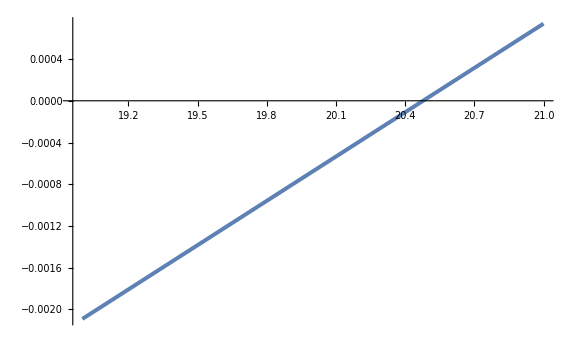

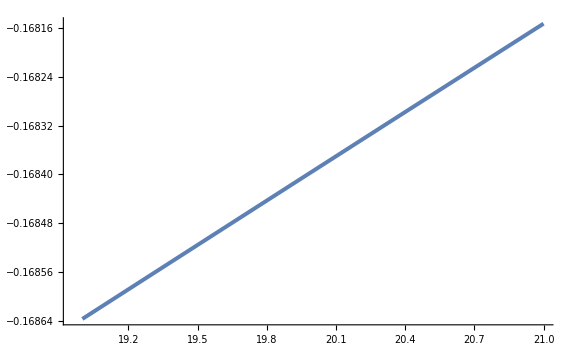

```mathematica
R1=Restimate1;
R2=Restimate2;
dR=dR1;
lambdas=ParallelTable[{R0,EvalSelectionFastArnoldi[(DD0 + EE0),R0,0.1,omegaestimate ,10][[-1]]},{R0,R1,R2,dR}];
gammas=Table[{lambdas[[i,1]],Re[lambdas[[i,2]]]},{i,1,Length[lambdas]}];
omegas=Table[{lambdas[[i,1]],Im[lambdas[[i,2]]]},{i,1,Length[lambdas]}];

ListPlot[gammas,PlotStyle->{Thickness[0.005]},TicksStyle->Large,AxesStyle->Thick,AxesLabel->{MaTeX["Ra ",Magnification->2],MaTeX["\\textrm{Re}\{\lambda\}",Magnification->2]},LabelStyle->{Large,Black},ImageSize->Large,PlotRange->All,Joined->True]

ListPlot[omegas,PlotStyle->{Thickness[0.005]},TicksStyle->Large,AxesStyle->Thick,AxesLabel->{MaTeX["Ra ",Magnification->2],MaTeX["\\textrm{Im}\{\lambda\}",Magnification->2]},LabelStyle->{Large,Black},ImageSize->Large,PlotRange->All,Joined->True]
```

#### Visual solver: direct (optional)

```mathematica
R1=Restimate1;
R2=Restimate2;
dR=dR1;
lambdas=ParallelTable[{R0,EvalSelection[(DD0 + EE0),R0,acc,dof][[2]]},{R0,R1,R2,dR}];
(*lambdas=ParallelTable[{R0,EvalSelection[Inverse[LL0].(DD0 + EE0),R0,acc,dof][[2]]},{R0,R1,R2,dR}];*)
(*lambdas=ParallelTable[{R0,EvalSelectionGeneralised[LL0,(DD0 + EE0),R0,acc,dof][[2]]},{R0,R1,R2,dR}];*)
gammas=Table[{lambdas[[i,1]],Re[lambdas[[i,2]]]},{i,1,Length[lambdas]}];
omegas=Table[{lambdas[[i,1]],Im[lambdas[[i,2]]]},{i,1,Length[lambdas]}];

ListPlot[gammas,PlotStyle->{Thickness[0.005]},TicksStyle->Large,AxesStyle->Thick,AxesLabel->{MaTeX["Ra ",Magnification->2],MaTeX["\\textrm{Re}\{\lambda\}",Magnification->2]},LabelStyle->{Large,Black},ImageSize->Large,PlotRange->All,Joined->True]

ListPlot[omegas,PlotStyle->{Thickness[0.005]},TicksStyle->Large,AxesStyle->Thick,AxesLabel->{MaTeX["Ra ",Magnification->2],MaTeX["\\textrm{Im}\{\lambda\}",Magnification->2]},LabelStyle->{Large,Black},ImageSize->Large,PlotRange->All,Joined->True]
```

-Graphics-

-Graphics-

#### Find critical Ra

```mathematica
R1 = SetPrecision[Rationalize[Restimate1],32];
R2= SetPrecision[Rationalize[Restimate2],32];
omegaest1= SetPrecision[Rationalize[omegaestimate],32];
```

```mathematica
(*out1=SecantMethod[ LL0,(DD0 +EE0)//N,dof,N[R1],N[R2],maxIter,acc] ;*)
out1=SecantMethodFastArnoldi[LL0,(DD0 +EE0),dof,R1,R2,omegaest1,maxIter,acc,accEV,Nsols];
RcBest=out1[[3]];
```

--------------------

Final Rc = 20.47756516363592

Final decay rate = 1.58578256309705510071925684076×10^-7

Final convection frequency = -0.168278787232867625849033864421

```mathematica
omegaBest=out1[[4]]
```

-0.168278787232867625849033864421

#### Find Eigenvector separately with Arnoldi

```mathematica
RcBest=SetPrecision[Rationalize[RcBest],32]//N;
omegaBest = SetPrecision[Rationalize[omegaBest],32];
```

```mathematica
eigvec=Eigensystem[SparseArray[(DD0+EE0)/.R0->RcBest],Nsols,Method->{"Arnoldi","Shift"->omegaBest  ⅈ(*,"StartingVector"->evecs[[try1]]*)(*,"BasisSize"->200*)(*,"MaxIterations"->1000*)(*,"Criteria"->"RealPart"*)}];
```

```mathematica
eigvec[[1]]
```

{1.58578×10^-7-0.168279 ⅈ,-0.141562-0.0632499 ⅈ,-0.0943408+0.00371138 ⅈ,-0.0910169-0.0211236 ⅈ,-0.0715641-0.00900626 ⅈ,-0.0266156-0.0598259 ⅈ,-0.0574917-0.0116832 ⅈ,-0.0442335-0.0139729 ⅈ,-0.0288946-0.0265526 ⅈ,-0.033476-0.017488 ⅈ}

```mathematica
posBest=Position[eigvec[[1]],MaximalBy[eigvec[[1]],Re][[1]]][[1]][[1]]
```

1

```mathematica
eigvecBest=eigvec[[2]][[posBest]];
```

```mathematica
Npeak=Position[Abs[eigvecBest[[1;;dof]]],Max[Abs[eigvecBest[[1;;dof]]]]]
```

{{1}}

### Find velocity eigenvalues (PG temperature)

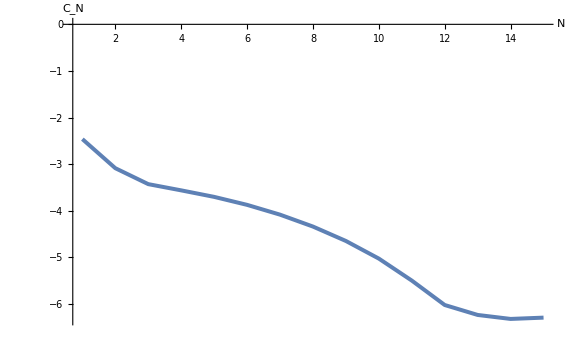

```mathematica
Cc2pg = eigvecBest[[1;;dof]];
ListLinePlot[Log[10,Abs[Cc2pg]],PlotRange->All,PlotStyle->{Directive[Thickness[0.005]],Directive[Dashed,Thickness[0.005]]},TicksStyle->Large,AxesStyle->Thick,AxesLabel->{"N","C_N"},LabelStyle->{Large,Black},ImageSize->Large]
```

```mathematica
psi2pg = s^m0 H^3Sum[Chop[Cc2pg,10^(-8)][[i]]Psi1[m0,i]Exp[ⅈ m0 phi]/H^3/s^m0,{i,1,dof}];
```

```mathematica
u2pg=H^2N[Sum[Chop[Cc2pg,10^(-8)][[i]]U1[s,phi,z,m0,i] Exp[ⅈ m0 phi]/H^2//Simplify,{i,1,dof}]]//Simplify;
```

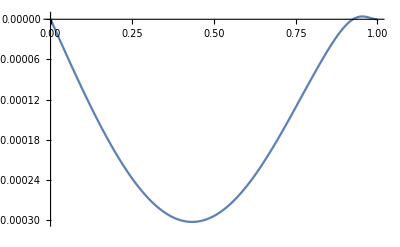

```mathematica
ListLinePlot[ParallelTable[{s,Re[psi2pg/.phi->0//Simplify]},{s,0,1,0.001}],PlotRange->All]
```

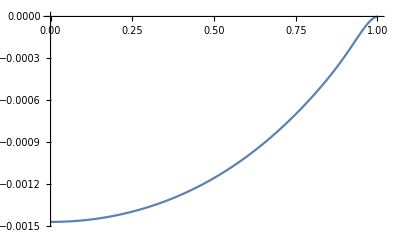

```mathematica
ListLinePlot[ParallelTable[{s,Re[u2pg[[1]]/.phi->0//Simplify]},{s,0,1,0.001}],PlotRange->All]
```

```mathematica
data=ParallelTable[With[{r=RandomReal[{0,1}],t=RandomReal[{0,2 Pi/4}]},{r Cos[t],r Sin[t],Re[psi2pg/.s->r/.phi->t]}],{Npoints}];
```

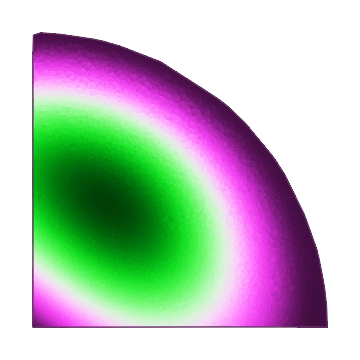

```mathematica
ListDensityPlot[data,Frame->False,BoundaryStyle->Automatic,PlotLegends->BarLegend[Automatic,LegendLabel->MaTeX["\\Psi",Magnification->2],LabelStyle->{Black,FontSize->20}],TicksStyle->{Large,Black},AxesStyle->Thick,LabelStyle->{Black,Large}(*,Contours->20,PlotRange->Full*),ImageSize->Medium,ColorFunction->"GreenPinkTones",PlotRange->All,InterpolationOrder->3,ClippingStyle->Automatic(*,MaxPlotPoints->50*)]
```

### Find temperature eigenvalues (PG temperature)

```mathematica
Abar2 = eigvecBest[[1+dof;;2*dof]];
```

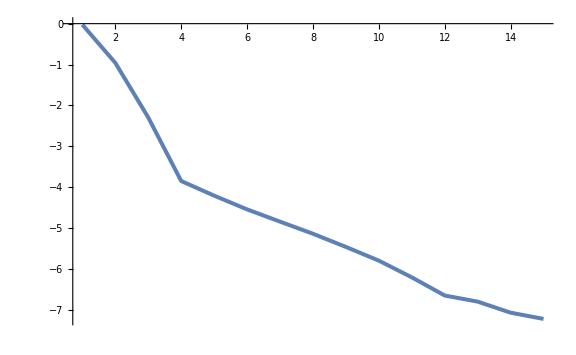

```mathematica
ListLinePlot[Log[10,Abs[Abar2]],PlotRange->All,PlotStyle->{Directive[Thickness[0.005]],Directive[Dashed,Thickness[0.005]]},TicksStyle->Large,AxesStyle->Thick,AxesLabel->{MaTeX["j",Magnification->2],MaTeX["\overline{A}_j",Magnification->2]},LabelStyle->{Large,Black},ImageSize->Large]
```

```mathematica
Atilde2 = eigvecBest[[1+2dof;;3*dof]];
```

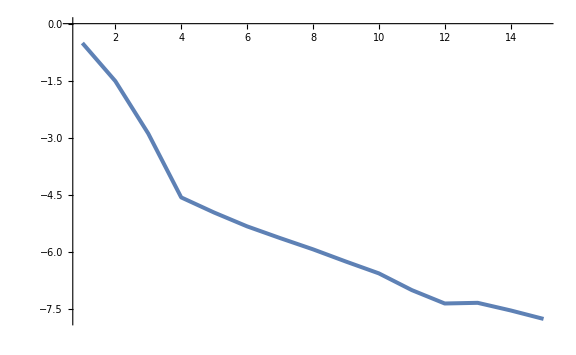

```mathematica
ListLinePlot[Log[10,Abs[Atilde2]],PlotRange->All,PlotStyle->{Directive[Thickness[0.005]],Directive[Dashed,Thickness[0.005]]},TicksStyle->Large,AxesStyle->Thick,AxesLabel->{MaTeX["j",Magnification->2],MaTeX["\widetilde{A}_j",Magnification->2]},LabelStyle->{Large,Black},ImageSize->Large]
```

```mathematica
Tbar2 = H^3Sum[Chop[Abar2,10^(-8)][[i]]Tbar1[m0,i]/H^3,{i,1,dof}];

zTtilde2 = H^4Sum[Chop[Atilde2,10^(-8)][[i]]zTtilde1[m0,i]/H^4,{i,1,dof}];
```

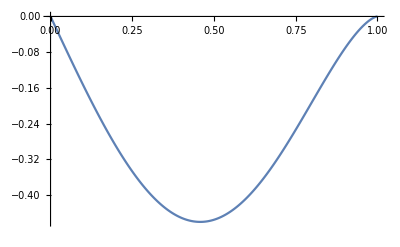

```mathematica
ListLinePlot[ParallelTable[{s,Re[Tbar2/.phi->0//Simplify]},{s,0,1,0.001}],PlotRange->All]
```

```mathematica
dataTbar=ParallelTable[With[{r=RandomReal[{0,1}],t=RandomReal[{0,2 Pi/4}]},{r Cos[t],r Sin[t],Re[Tbar2/.s->r/.phi->t]}],{Npoints}];
```

```mathematica
dataTtilde=ParallelTable[With[{r=RandomReal[{0,1}],t=RandomReal[{0,2 Pi/4}]},{r Cos[t],r Sin[t],Re[zTtilde2/.s->r/.phi->t]}],{Npoints}];
```

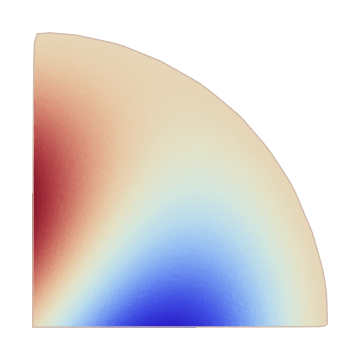

```mathematica
ListDensityPlot[dataTbar,Frame->False,BoundaryStyle->Automatic,PlotLegends->BarLegend[Automatic,LegendLabel->MaTeX["\\overline{T}",Magnification->2],LabelStyle->{Black,FontSize->20}],TicksStyle->{Large,Black},AxesStyle->Thick,LabelStyle->{Black,Large}(*,Contours->20,PlotRange->Full*),ImageSize->Medium,ColorFunction->"ThermometerColors",PlotRange->All,InterpolationOrder->3,ClippingStyle->Automatic(*,MaxPlotPoints->50*)]
```

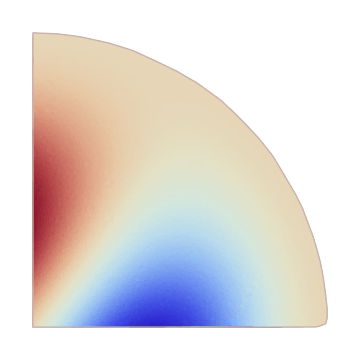

```mathematica
ListDensityPlot[dataTtilde,Frame->False,BoundaryStyle->Automatic,PlotLegends->BarLegend[Automatic,LegendLabel->MaTeX["\\widetilde{zT}",Magnification->2],LabelStyle->{Black,FontSize->20}],TicksStyle->{Large,Black},AxesStyle->Thick,LabelStyle->{Black,Large}(*,Contours->20,PlotRange->Full*),ImageSize->Medium,ColorFunction->"ThermometerColors",PlotRange->All,InterpolationOrder->3,ClippingStyle->Automatic(*,MaxPlotPoints->50*)]
```